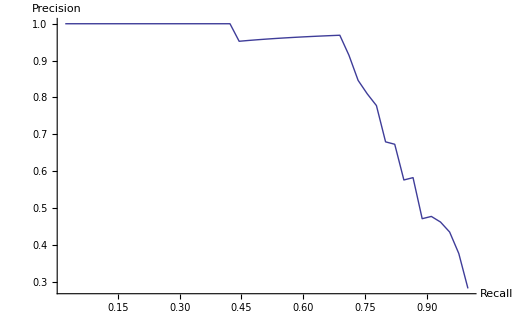

```mathematica
(* Import file *)
import=Import["C:\\Temp\\Computation\\CARS\\AUDIAVUS\\AUDIAVUS_dist.txt","Table"];
class="CARS";
GetClass[s_]:=StringTake[s,First[First[StringPosition[s,"/",1]]]-1]; (* late binding!! *)

(* Get c - cluster size *)
c=0;
For[i=0,i<Length[import],i++;
s=import⟦i⟧⟦2⟧;
s=GetClass[s];
If[s==class,c++];
];

(* Precision Recall *)
data ={};
recalled=0;
recall=0;
For[i=0,i<Length[import],i++;
s=import⟦i⟧⟦2⟧;
s=StringTake[s,First[First[StringPosition[s,"/",1]]]-1];
If[s==class,recalled++];
If[recalled/c>recall,
recall=recalled/c;
precision=recalled/i;
data=Append[data,{recall,precision}];
];
];
ListPlot[data,AxesOrigin->{0,0},Joined->True,AxesLabel->{"Recall","Precision"}]
```